Evidence of H_1, P(D|H_1)

```mathematica
Clear[x,y,t,w1,w0]
```

```mathematica
data={{-8,8},{-2,10},{6,11}};
```

```mathematica
y=w0+w1 x;
```

```mathematica
w1=0;∫_(-∞)^∞ √(1/(2π))Exp[(-(y-t)^2)/2] √(1/(2π))Exp[(-(w0)^2)/2]ⅆw0
```

```mathematica
(ⅇ^(-t^2/4))/(2 √π)/.t->{8,10,11}//N
```

{3.17456×10^-8,3.91772×10^-12,2.05583×10^-14}

```mathematica
L1={3.1745586679666396*^-8,3.917716632754334*^-12,2.0558290113157305*^-14};
```

```mathematica
evidence1=Product[L1[[i]],{i,1,3}]
```

2.55684×10^-33

Evidence of H_2, P(D|H_2)

```mathematica
Clear[w0,w1,x,y,t]
```

```mathematica
y=w0+w1 x;
```

```mathematica
√(1/(2π))Exp[(-(t-y)^2)/2] √(1/(2π))Exp[-w1^2/2] √(1/(2π))Exp[(-(w0)^2)/2]
```

(ⅇ^(-w0^2/2-w1^2/2-1/2 (t-w0-w1 x)^2))/(2 √2 π^(3/2))

```mathematica
∫_(-∞)^∞ ∫_(-∞)^∞ √(1/(2π))Exp[(-(t-y)^2)/2] √(1/(2π))Exp[-w1^2/2] √(1/(2π))Exp[(-(w0)^2)/2]ⅆw1ⅆw0
```

ConditionalExpression[(ⅇ^(-t^2/(4+2 x^2)))/(√(2 π) √(1+x^2) √(1+1/(1+x^2))),Re[1/(1+x^2)]≥-1]

```mathematica
(ⅇ^(-t^2/(4+2 x^2)))/(√(2 π) √(1+x^2) √(1+1/(1+x^2)))/.{{x->-8,t->8},{x->-2,t->10},{x->6,t->11}}//N
```

{0.0302393,0.0000391484,0.0131697}

```mathematica
L2={0.03023925424859377,0.00003914837665445475,0.013169695605323387};
```

```mathematica
evidence2=Product[L2[[i]],{i,1,3}]
```

1.55905×10^-8

Linear Regression and evidence from the best fit

```mathematica
data={{-8,8},{-2,10},{6,11}}
```

{{-8,8},{-2,10},{6,11}}

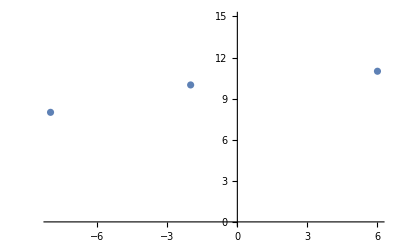

```mathematica
P1=ListPlot[data, PlotRange->{0,15}]
```

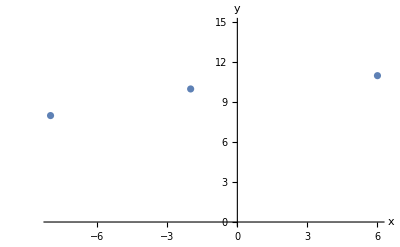

```mathematica
Show[P1,AxesLabel->{HoldForm[x],HoldForm[y]},PlotRange->{0,15},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
model=LinearModelFit[data,x,x]
```

FittedModel[9.94595+0.209459 x]

```mathematica
model["BestFit"]
```

9.94595+0.209459 x

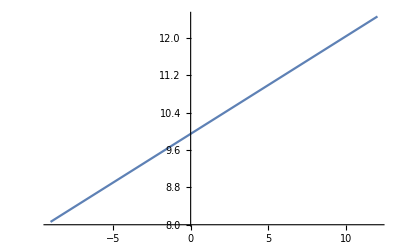

```mathematica
P2=Plot[9.945945945945946+0.20945945945945946 x,{x,-9,12}]
```

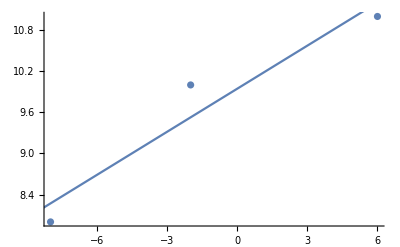

```mathematica
Show[P1,P2]
```

```mathematica
9.945945945945946+0.20945945945945946 x/.x->{-8,-2,6}
```

{8.27027,9.52703,11.2027}

```mathematica
{8.27027027027027,9.527027027027026,11.202702702702702}-{8,10,11}
```

{0.27027,-0.472973,0.202703}

```mathematica
1/(2π)Exp[-(δ)^2] 1/(2π)/.δ->{0.2702702702702702,-0.4729729729729737,0.20270270270270174}//N
```

{0.023546,0.0202529,0.0243106}

```mathematica
L0={0.02354598051605746,0.02025289432564488,0.0243106070806057};
```

```mathematica
evidence0=Product[L0[[i]],{i,1,3}]
```

0.0000115931

Ratio of evidences

```mathematica
evidence0/evidence1
```

4.53415×10^27

```mathematica
evidence0/evidence2
```

743.6

```mathematica
evidence2/evidence1
```

6.09758×10^24